```mathematica
(* 01 *)
Manipulate[
x^2+1,
{x,1,10}
]
```

```mathematica
(* 02 *)
Manipulate[
{x,x^2+1,x^3+1},
{x,1,10}
]
```

```mathematica
(* 03 *)
Manipulate[
{x,x^2+1,x^3+1, x^2> 2x+1},
{x,1,10}
]
```

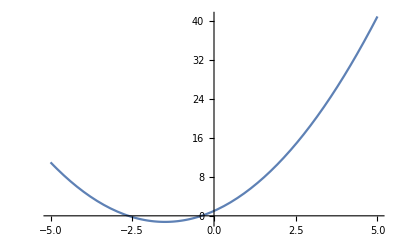

```mathematica
(* 04 *)
Plot[x^2+3x+1,{x,-5,5}]
```

```mathematica
(* 05 *)
Manipulate[
Plot[c x^2+3x+1,{x,-5,5}],
{c,1,20,Appearance->"Labeled"}
]
```

```mathematica
(* 06 *)
Manipulate[
Plot[c x^2+3x+1,{x,-5,5},PlotRange->{-5,100}],
{c,1,20,Appearance->"Labeled"}
]
```

```mathematica
(* 07 *)
Manipulate[
Plot[c x^2+3d x+1,{x,-5,5},PlotRange->{-5,100}],
{c,0,20,Appearance->"Labeled"},
{d,0,20,Appearance->"Labeled"}
]
```

```mathematica
(* 08 *)
Manipulate[
Plot[{c x^2+3d x+1,2 c x^2 -d x +3},{x,-5,5},PlotRange->{-5,100}],
{c,0,20,Appearance->"Labeled"},
{d,0,20,Appearance->"Labeled"}
]
```

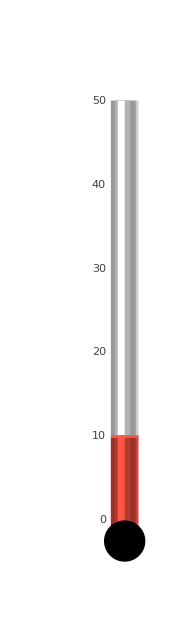

```mathematica
(* 09 *)
ThermometerGauge[10,{0,50}]
```

```mathematica
(* 10 *)
Manipulate[
	ThermometerGauge[10 x,{0,50}],
	{x,0,5}
]
```